### Distribution for ϕ

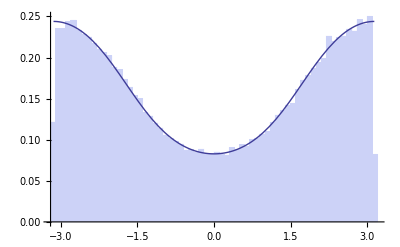

```mathematica
Clear;
ClearAll;
SetDirectory["~/Projects/Paths/control/main/output"];
phis=Import["phis.dat"];
R=1;
m=phis[[1]][[1]];
λ=phis[[1]][[2]];
rho = phis[[1]][[3]];
c = Sqrt[m^2-λ^2];
phis=Flatten[Delete[phis,1]];
histophi=Histogram[phis,50,"PDF"];
B = Sqrt[R^2-rho^2 Sin[phi]^2]-rho*Cos[phi];
plotphi=Plot[1/(2π)(1- c B BesselK[1,c B])/(1-c R BesselI[0,rho c]BesselK[1,R c]),{phi,Min[phis],Max[phis]}];
Show[{histophi,plotphi}]
```

### Distribution for ξ

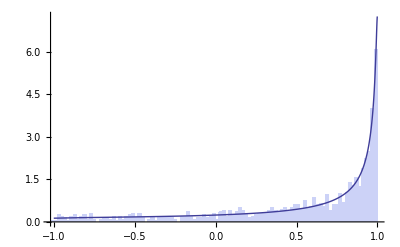

```mathematica
Clear;
ClearAll;
SetDirectory["~/Projects/Paths/control/main/output"];
xis=Import["xis.dat"];
R=1;
m=xis[[1]][[1]];
λ=xis[[1]][[2]];
rho = xis[[1]][[3]];
phi = xis[[1]][[4]];
c = Sqrt[m^2-λ^2];
xis=Flatten[Delete[xis,1]];
histoxi=Histogram[xis,100,"PDF"];
B = Sqrt[R^2-rho^2 Sin[phi]^2]-rho*Cos[phi];
plotxi=Plot[(1-(1+(m-λ xi)*(B/Sqrt[1-xi^2]))*Exp[-(m-λ xi)*(B/Sqrt[1-xi^2])])/((m-λ xi)^2 2/c^2*(1-B*c*BesselK[1,B*c])),{xi,Min[xis],Max[xis]},PlotRange->Full];
Show[{histoxi,plotxi}]
```

### Distribution for ρ’ given ρ

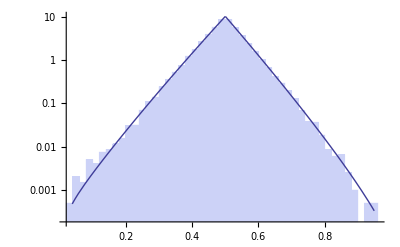

```mathematica
Clear;
ClearAll;
SetDirectory["~/Projects/Paths/control/main/output"];
rhos=Import["rhos.dat"];
R=1;
m=rhos[[1]][[1]];
λ=rhos[[1]][[2]];
ρ = rhos[[1]][[3]];
c = Sqrt[m^2-λ^2];
rhos=Flatten[Delete[rhos,1]];
historho=Histogram[rhos,50,"PDF",ScalingFunctions->{None,"Log"}];
plotrho=LogPlot[m^2 rho BesselJ[0,λ rho]/BesselJ[0,λ ρ] BesselI[0,c*Min[{rho,ρ}]]*BesselK[0,c*Max[{rho,ρ}]],{rho,Min[rhos],Max[rhos]}, PlotRange->Full];
Show[{historho,plotrho}]
```

### Generating function for longitudinal jumps z’-z

```mathematica
Clear;
ClearAll;
SetDirectory["~/Projects/Paths/control/main/output"];
ltzs=Import["ltzs.dat"];
R=1;
m=ltzs[[1]][[1]];
λ=ltzs[[1]][[2]];
smin=ltzs[[1]][[3]];
smax=ltzs[[1]][[4]];
c = Sqrt[m^2-λ^2];
ltzs=Delete[ltzs,1];
```

```mathematica
u = Sqrt[m^2-(s+λ)^2];
LT=m^2/(m^2-s^2-2λ s)*(1 + λ R BesselI[1,R u]*(λ/u BesselK[0,R u] - BesselJ[0,λ R]/BesselJ[1,λ R] BesselK[1,R u]));
```

```mathematica
plotnum=ListLogPlot[ltzs,Joined->True, PlotRange->{{smin,smax},Automatic},PlotStyle->Red];
plot=Plot[Log[LT], {s,smin, smax}];
asd=ListPlot[{{m-λ,0}},PlotStyle->{PointSize->.03}];
Show[{plot,plotnum,asd}]
```

### Distribution for longitudinal jumps z’-z

```mathematica
Clear;
ClearAll;
SetDirectory["~/Projects/Paths/control/main/output"];
deltazs=Import["deltazs.dat"];
R=1;
m=deltazs[[1]][[1]];
λ=deltazs[[1]][[2]];
c = Sqrt[m^2-λ^2];
deltazs=Flatten[Delete[deltazs,1]];
minz = Min[deltazs];
maxz = Max[deltazs];
```

```mathematica
u = Sqrt[m^2-(s+λ)^2];
LT=m^2/(m^2-s^2-2λ s)*(1 + λ R BesselI[1,R u]*(λ/u BesselK[0,R u] - BesselJ[0,λ R]/BesselJ[1,λ R] BesselK[1,R u]));
normz=1/LT/.s->0;
r =Sqrt[m^2+λ^2];
pdfz[deltaz_?NumericQ]:=Re[normz/(2π)*NIntegrate[LT*Exp[-s deltaz]/.s->I k, {k, -∞, ∞}]//Quiet];
tabz=Table[{deltaz,pdfz[deltaz]},{deltaz,minz,maxz,(maxz-minz)/100}];
```

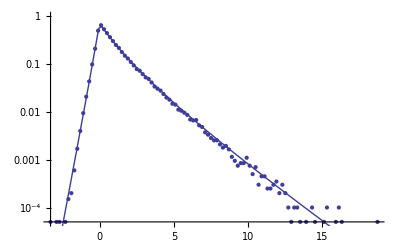

```mathematica
plotright=LogPlot[Exp[-(Sqrt[m^2+λ^2]-λ)deltaz],{deltaz,0,maxz}];
plotleft=LogPlot[Exp[(Sqrt[m^2+λ^2]+λ)deltaz],{deltaz,minz,0}];
plotlong=LogPlot[Exp[-(m-λ) deltaz],{deltaz,0,maxz}];
(*histoz=Histogram[deltazs,100,"PDF", ScalingFunctions->{None,"Log"}];*)
{bins,heights} = N[HistogramList[deltazs,100,"PDF"]];
histoz=ListLogPlot[Table[{(bins[[i]]+bins[[i+1]])/2,heights[[i]](**Exp[-3*bins[[i]]]*)},{i,1,Length[heights]}]];
plotz=ListLogPlot[tabz,Joined->True];
Show[{histoz,plotz}]
```